# (4) Gravitational perturbations: Regge-Wheeler Equation (Odd parity)

## Reference: E. Berti’s Black Hole Perturbation Theory Notes (ICTS) [https://www.icts.res.in/event/page/3071] Equation numbers cited throughout this document follow the numbering convention used in these notes to facilitate cross-referencing.

## (0) Set-up

```mathematica
SetDirectory["C:\Program Files\Wolfram Research\Mathematica\12.1\AddOns\Applications\xAct_1.2.0"];
```

```mathematica
<<xAct`xPert`(*perturbation theory*)
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
<<xAct`xCoba`(*tensor component calculations*)
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<MaTeX` ;(*LaTeX integration in text and output cells*)
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
SetOptions[MaTeX,FontSize->14];
```

```mathematica
mt = MaTeX;
```

Syntax to generate MaTeX formatted numbered equations:  “<expression>  \qquad   <equation_number> “ // mt
Execute the above in an input cell, and then paste result in a text cell.

```mathematica
$DefInfoQ=False;  (*turns off optional xAct messages*)
```

## (I) Definitions

```mathematica
DefManifold[M,4,IndexRange[a,f]]
```

```mathematica
DefMetric[-1,g[-a,-b],CD]
```

```mathematica
DefChart[B,M,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Define metric perturbation

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

Notational clean-up

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[K]^="F";
PrintAs[EinsteinCD]^="G";
$CovDFormat="Prefix";
PrintAs[Detg]^= "g";
```

#### Deriving the Einstein field equations

The Einstein-Hilbert action is:

```mathematica
L=Sqrt[-Detg[]](RicciScalarCD[])
```

√-g R

First order variation in L

```mathematica
Lpert=L//Perturbation//ExpandPerturbation
```

-(g h | 1 |   | a
  | a |   R)/(2 √-g)+√-g (-h | 1 | a | b
  |   |   R |   |  
a | b+g | a | b
  |   (1/2 (-(▽_a▽_b h | 1 | c |  
  |   | c)-▽_a▽_c h | 1 | c |  
  |   | b+▽_a▽^c h | 1 |   |  
  | b | c)+1/2 (▽_c▽_a h | 1 | c |  
  |   | b+▽_c▽_b h | 1 | c |  
  |   | a-▽_c▽^c h | 1 |   |  
  | b | a)))

```mathematica
tempMet1 =Lpert//VarD[h[LI[1],a,b],CD]
```

-δ |   | 1
1 |   √-g R |   |  
a | b+1/2 δ |   | 1
1 |   √-g g |   |  
a | b R

Substituting the value of the Kronecker delta component, δ |   | 1
1 |   = 1

```mathematica
tempMet2 = tempMet1/.delta[-LI[1],LI[1]]->1;
```

Since field equations are derived by imposing that the variation in action is zero, we can simplify our expression by multiplying with factor of 1/Sqrt[-Detg[]]

```mathematica
equationMetric = (-1/Sqrt[-Detg[]])tempMet2//Expand//ToCanonical//ContractMetric
```

R |   |  
a | b-1/2 g |   |  
a | b R

It follows that the vacuum Einstein equation is:

```mathematica
einsteinEqn = equationMetric==0
```

R |   |  
a | b-1/2 g |   |  
a | b R==0

## (II) Perturbations

```mathematica
pert1=einsteinEqn//First//Perturbation//ExpandPerturbation//Expand
```

1/2 g |   |  
a | b h | 1 | c | d
  |   |   R |   |  
c | d-1/2 h | 1 |   |  
  | a | b R-1/2 (▽_a▽_b h | 1 | c |  
  |   | c)-1/2 (▽_a▽_c h | 1 | c |  
  |   | b)+1/2 (▽_a▽^c h | 1 |   |  
  | b | c)+1/2 (▽_c▽_a h | 1 | c |  
  |   | b)+1/2 (▽_c▽_b h | 1 | c |  
  |   | a)-1/2 (▽_c▽^c h | 1 |   |  
  | b | a)+1/4 g |   |  
a | b g | c | d
  |   (▽_c▽_d h | 1 | e |  
  |   | e)+1/4 g |   |  
a | b g | c | d
  |   (▽_c▽_e h | 1 | e |  
  |   | d)-1/4 g |   |  
a | b g | c | d
  |   (▽_c▽^e h | 1 |   |  
  | d | e)-1/4 g |   |  
a | b g | c | d
  |   (▽_e▽_c h | 1 | e |  
  |   | d)-1/4 g |   |  
a | b g | c | d
  |   (▽_e▽_d h | 1 | e |  
  |   | c)+1/4 g |   |  
a | b g | c | d
  |   (▽_e▽^e h | 1 |   |  
  | d | c)

```mathematica
pert2 = pert1//ToCanonical//ContractMetric//SeparateMetric[g]
```

1/2 g |   |  
a | b g | c | e
  |   g | d | f
  |   h | 1 |   |  
  | e | f R |   |  
c | d-1/2 h | 1 |   |  
  | a | b R-1/2 g | c | d
  |   (▽_a▽_b h | 1 |   |  
  | d | c)+1/2 g | c | d
  |   (▽_c▽_a h | 1 |   |  
  | b | d)+1/2 g | c | d
  |   (▽_c▽_b h | 1 |   |  
  | a | d)-1/2 g | c | d
  |   (▽_c▽_d h | 1 |   |  
  | a | b)+1/4 g |   |  
a | b g | c | f
  |   g | d | e
  |   (▽_c▽_f h | 1 |   |  
  | e | d)-1/2 g |   |  
a | b g | c | e
  |   g | d | f
  |   (▽_d▽_c h | 1 |   |  
  | e | f)+1/4 g |   |  
a | b g | c | e
  |   g | d | f
  |   (▽_d▽_f h | 1 |   |  
  | c | e)

### Background components

Define the background metric components () - Schwarzschild:

```mathematica
DefScalarFunction[fmet, PrintAs->"f"]
```

```mathematica
bg=CTensor[{
{-fmet[r[]],0,0,0},
{0,1/(fmet[r[]]),0,0},
{0,0,r[]^2,0},
{0,0,0,r[]^2Sin[θ[]]^2}
},{-B,-B}]
```

CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]

Inverse of the background metric ():

```mathematica
invbg=Inv[bg]
```

CTensor[{{-1/f[r],0,0,0},{0,f[r],0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}},{B,B},0]

Christoffel symbols () of the background metric:

```mathematica
CDbg=LC[bg]
```

CCovD[PDB,CTensor[{{{0,f'[r]/(2 f[r]),0,0},{f'[r]/(2 f[r]),0,0,0},{0,0,0,0},{0,0,0,0}},{{1/2 f[r] f'[r],0,0,0},{0,-f'[r]/(2 f[r]),0,0},{0,0,-f[r] r,0},{0,0,0,-f[r] r Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}},{B,-B,-B},0],CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

```mathematica
PDbg=PD[bg]
```

PD[CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

Ricci tensor () of the background metric:

```mathematica
RicciCDbg=Ricci[CDbg]
```

CTensor[{{1/2 f[r] ((2 f'[r])/r+f''[r]),0,0,0},{0,-(2 f'[r]+r f''[r])/(2 f[r] r),0,0},{0,0,1-f[r]-r f'[r],0},{0,0,0,-Sin[θ]^2 (-1+f[r]+r f'[r])}},{-B,-B},0]

Einstein tensor () of the background metric:

```mathematica
EinsteinCDbg=Einstein[CDbg]
```

CTensor[{{-(f[r] (-1+f[r]+r f'[r]))/r^2,0,0,0},{0,(-1+f[r]+r f'[r])/(f[r] r^2),0,0},{0,0,1/2 r (2 f'[r]+r f''[r]),0},{0,0,0,1/2 r Sin[θ]^2 (2 f'[r]+r f''[r])}},{-B,-B},0]

Ricci scalar () of the background metric:

```mathematica
ScalarCDbg=RicciScalar[CDbg]
```

CTensor[-(-2+2 f[r]+4 r f'[r]+r^2 f''[r])/r^2,{},0]

```mathematica
$LargeComponentSize=10000 (*Allows large cTensor output *);
```

Define the spherical harmonic function, Ylm

```mathematica
DefScalarFunction[Ylm, PrintAs->"Y_lm"]
```

Define all the axial perturbation functions

```mathematica
DefScalarFunction[h0, PrintAs->"h_0"]
DefScalarFunction[h1, PrintAs->"h_1"]
```

```mathematica
pertAx=
CTensor[{
{0,0,(h0[t[],r[]]/Sin[θ[]])D[Ylm[θ[],ϕ[]],ϕ[]],-h0[t[],r[]]Sin[θ[]]D[Ylm[θ[],ϕ[]],θ[]]},
{0,0,(h1[t[],r[]]/Sin[θ[]])D[Ylm[θ[],ϕ[]],ϕ[]],-h1[t[],r[]]Sin[θ[]]D[Ylm[θ[],ϕ[]],θ[]]},
{(h0[t[],r[]]/Sin[θ[]])D[Ylm[θ[],ϕ[]],ϕ[]],(h1[t[],r[]]/Sin[θ[]])D[Ylm[θ[],ϕ[]],ϕ[]],0,0},
{-h0[t[],r[]]Sin[θ[]]D[Ylm[θ[],ϕ[]],θ[]],-h1[t[],r[]]Sin[θ[]]D[Ylm[θ[],ϕ[]],θ[]],0,0}
}, {-B,-B}]
```

CTensor[{{0,0,Csc[θ] h_0[t,r] Y_lm^(0,1)[θ,ϕ],-h_0[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ]},{0,0,Csc[θ] h_1[t,r] Y_lm^(0,1)[θ,ϕ],-h_1[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ]},{Csc[θ] h_0[t,r] Y_lm^(0,1)[θ,ϕ],Csc[θ] h_1[t,r] Y_lm^(0,1)[θ,ϕ],0,0},{-h_0[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ],-h_1[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ],0,0}},{-B,-B},0]

```mathematica
componentRules= {
  g[-a_Symbol, -b_Symbol] :> bg[-a, -b],
  g[a_Symbol, b_Symbol] :> invbg[a, b],
  CD[-a_Symbol] :> CDbg[-a],
  PD[-a_Symbol] :> PDbg[-a],
  RicciCD[-a_Symbol, -b_Symbol] :> RicciCDbg[-a, -b],
  RicciScalarCD[] :> ScalarCDbg[],
  EinsteinCD[-a_Symbol, -b_Symbol] :> EinsteinCDbg[-a, -b],
h[LI[1],-a_Symbol,-b_Symbol]:> pertAx[-a,-b]
  }
```

{g |   |  
a̲ | b̲:>bg[-a,-b],g | a̲ | b̲
  |  :>invbg[a,b],CD[-a_Symbol]:>CDbg[-a],PD[-a_Symbol]:>PDbg[-a],R |   |  
a̲ | b̲:>RicciCDbg[-a,-b],R:>ScalarCDbg[],G |   |  
a̲ | b̲:>EinsteinCDbg[-a,-b],h | 1 |   |  
  | a̲ | b̲:>pertAx[-a,-b]}

```mathematica
pertMatrix1 = pert2/.componentRules//ContractBasis//ToBasis[B]//ComponentArray//Simplify;
```

```mathematica
pertMatrix1//MatrixForm
```

(0 | 0 | -(Csc[θ] (f[r] r Y_lm^(0,1)[θ,ϕ] (r h_0^(0,2)[t,r]-2 h_1^(1,0)[t,r]-r h_1^(1,1)[t,r])+h_0[t,r] (-(-2+2 f[r]+2 r f'[r]+r^2 f''[r]) Y_lm^(0,1)[θ,ϕ]+Csc[θ]^2 Y_lm^(0,3)[θ,ϕ]+Cot[θ] Y_lm^(1,1)[θ,ϕ]+Y_lm^(2,1)[θ,ϕ])))/(2 r^2) | (Sin[θ] (f[r] r Y_lm^(1,0)[θ,ϕ] (r h_0^(0,2)[t,r]-2 h_1^(1,0)[t,r]-r h_1^(1,1)[t,r])+h_0[t,r] (-2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(-2+Csc[θ]^2+2 f[r]+2 r f'[r]+r^2 f''[r]) Y_lm^(1,0)[θ,ϕ]+Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+Cot[θ] Y_lm^(2,0)[θ,ϕ]+Y_lm^(3,0)[θ,ϕ])))/(2 r^2)
0 | 0 | -(Csc[θ] (r Y_lm^(0,1)[θ,ϕ] (-2 h_0^(1,0)[t,r]+r (h_0^(1,1)[t,r]-h_1^(2,0)[t,r]))+f[r] h_1[t,r] (-(-2+2 r f'[r]+r^2 f''[r]) Y_lm^(0,1)[θ,ϕ]+Csc[θ]^2 Y_lm^(0,3)[θ,ϕ]+Cot[θ] Y_lm^(1,1)[θ,ϕ]+Y_lm^(2,1)[θ,ϕ])))/(2 f[r] r^2) | (Sin[θ] (r Y_lm^(1,0)[θ,ϕ] (-2 h_0^(1,0)[t,r]+r (h_0^(1,1)[t,r]-h_1^(2,0)[t,r]))+f[r] h_1[t,r] (-2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(-2+Csc[θ]^2+2 r f'[r]+r^2 f''[r]) Y_lm^(1,0)[θ,ϕ]+Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+Cot[θ] Y_lm^(2,0)[θ,ϕ]+Y_lm^(3,0)[θ,ϕ])))/(2 f[r] r^2)
-(Csc[θ] (f[r] r Y_lm^(0,1)[θ,ϕ] (r h_0^(0,2)[t,r]-2 h_1^(1,0)[t,r]-r h_1^(1,1)[t,r])+h_0[t,r] (-(-2+2 f[r]+2 r f'[r]+r^2 f''[r]) Y_lm^(0,1)[θ,ϕ]+Csc[θ]^2 Y_lm^(0,3)[θ,ϕ]+Cot[θ] Y_lm^(1,1)[θ,ϕ]+Y_lm^(2,1)[θ,ϕ])))/(2 r^2) | -(Csc[θ] (r Y_lm^(0,1)[θ,ϕ] (-2 h_0^(1,0)[t,r]+r (h_0^(1,1)[t,r]-h_1^(2,0)[t,r]))+f[r] h_1[t,r] (-(-2+2 r f'[r]+r^2 f''[r]) Y_lm^(0,1)[θ,ϕ]+Csc[θ]^2 Y_lm^(0,3)[θ,ϕ]+Cot[θ] Y_lm^(1,1)[θ,ϕ]+Y_lm^(2,1)[θ,ϕ])))/(2 f[r] r^2) | -(Csc[θ] (f[r] h_1[t,r] f'[r]+f[r]^2 h_1^(0,1)[t,r]-h_0^(1,0)[t,r]) (Cot[θ] Y_lm^(0,1)[θ,ϕ]-Y_lm^(1,1)[θ,ϕ]))/f[r] | (Sin[θ] (f[r] h_1[t,r] f'[r]+f[r]^2 h_1^(0,1)[t,r]-h_0^(1,0)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]-Y_lm^(2,0)[θ,ϕ]))/(2 f[r])
(Sin[θ] (f[r] r Y_lm^(1,0)[θ,ϕ] (r h_0^(0,2)[t,r]-2 h_1^(1,0)[t,r]-r h_1^(1,1)[t,r])+h_0[t,r] (-2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(-2+Csc[θ]^2+2 f[r]+2 r f'[r]+r^2 f''[r]) Y_lm^(1,0)[θ,ϕ]+Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+Cot[θ] Y_lm^(2,0)[θ,ϕ]+Y_lm^(3,0)[θ,ϕ])))/(2 r^2) | (Sin[θ] (r Y_lm^(1,0)[θ,ϕ] (-2 h_0^(1,0)[t,r]+r (h_0^(1,1)[t,r]-h_1^(2,0)[t,r]))+f[r] h_1[t,r] (-2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(-2+Csc[θ]^2+2 r f'[r]+r^2 f''[r]) Y_lm^(1,0)[θ,ϕ]+Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+Cot[θ] Y_lm^(2,0)[θ,ϕ]+Y_lm^(3,0)[θ,ϕ])))/(2 f[r] r^2) | (Sin[θ] (f[r] h_1[t,r] f'[r]+f[r]^2 h_1^(0,1)[t,r]-h_0^(1,0)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]-Y_lm^(2,0)[θ,ϕ]))/(2 f[r]) | ((f[r] h_1[t,r] f'[r]+f[r]^2 h_1^(0,1)[t,r]-h_0^(1,0)[t,r]) (Cos[θ] Y_lm^(0,1)[θ,ϕ]-Sin[θ] Y_lm^(1,1)[θ,ϕ]))/f[r])

```mathematica
coordFuncReplace = {r[]->r,t[]->t, θ[]->θ,ϕ[]->ϕ}
```

{r→r,t→t,θ→θ,ϕ→ϕ}

```mathematica
DefConstantSymbol[l]
```

```mathematica
DefConstantSymbol[m]
```

```mathematica
assocLegendre = {Csc[θ]^2*Derivative[0,2][Ylm][θ,ϕ]+Cot[θ]*Derivative[1,0][Ylm][θ,ϕ]+Derivative[2,0][Ylm][θ,ϕ]->-(l*(1+l)*Ylm[θ,ϕ]) }
```

{Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]→-l (1+l) Y_lm[θ,ϕ]}

```mathematica
pertMatrix = pertMatrix1/.coordFuncReplace;
```

```mathematica
pertThetaPhi=pertMatrix [[3,4]]==0//Simplify//First
```

(Sin[θ] (f[r] h_1[t,r] f'[r]+f[r]^2 h_1^(0,1)[t,r]-h_0^(1,0)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]-Y_lm^(2,0)[θ,ϕ]))/f[r]

```mathematica
DefConstantSymbol[mass, PrintAs->"M"]
```

```mathematica
massRule={fmet[r]->1-(2*M)/r, Derivative[1][fmet][r]->(2*M)/r^2, 
Derivative[2][fmet][r]->(-4*M)/r^3}
```

{f[r]→1-(2 M)/r,f'[r]→(2 M)/r^2,f''[r]→-(4 M)/r^3}

```mathematica
DefConstantSymbol[om, PrintAs-> "ω"]
```

Assume harmonic time dependence,  e^(-i ω t)

```mathematica
harmonicTime = {Derivative[1, 0][h0][t, r] -> -I *om* h0[t, r]}
```

{h_0^(1,0)[t,r]→-ⅈ ω h_0[t,r]}

```mathematica
temp1=pertThetaPhi/.massRule/.harmonicTime//Simplify
```

(Sin[θ] (-ⅈ ω r^3 h_0[t,r]+(2 M-r) (2 M h_1[t,r]+r (-2 M+r) h_1^(0,1)[t,r])) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]-Y_lm^(2,0)[θ,ϕ]))/((2 M-r) r^2)

```mathematica
temp2 = temp1/(-1/((2 M-r) r^2)Sin[θ])//Expand//Simplify
```

(ⅈ ω r^3 h_0[t,r]+(2 M-r) (-2 M h_1[t,r]+(2 M-r) r h_1^(0,1)[t,r])) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]-Y_lm^(2,0)[θ,ϕ])

```mathematica
temp3= temp2/((Csc[θ]^2 Derivative[0,2][Subscript[Y, lm]][θ,ϕ]+Cot[θ] Derivative[1,0][Subscript[Y, lm]][θ,ϕ]-Derivative[2,0][Subscript[Y, lm]][θ,ϕ]))
```

ⅈ ω r^3 h_0[t,r]+(2 M-r) (-2 M h_1[t,r]+(2 M-r) r h_1^(0,1)[t,r])

```mathematica
Eq1 = temp3==0
```

ⅈ ω r^3 h_0[t,r]+(2 M-r) (-2 M h_1[t,r]+(2 M-r) r h_1^(0,1)[t,r])==0

This corresponds to (Eq: 4.4.71).

Solve for h_0

```mathematica
h0rule = Solve[Eq1,h0[t,r]]//Simplify//First
```

{h_0[t,r]→(ⅈ (2 M-r) (-2 M h_1[t,r]+(2 M-r) r h_1^(0,1)[t,r]))/(ω r^3)}

Identify as (Eq: 4.4.72).

```mathematica
h0val[r] = h0[t,r]/.h0rule
```

(ⅈ (2 M-r) (-2 M h_1[t,r]+(2 M-r) r h_1^(0,1)[t,r]))/(ω r^3)

```mathematica
h0prime = D[h0val[r],r]//Simplify
```

(ⅈ (4 M (3 M-r) h_1[t,r]+(2 M-r) r (-6 M h_1^(0,1)[t,r]+(2 M-r) r h_1^(0,2)[t,r])))/(ω r^4)

```mathematica
h0primerule = {Derivative[0,1][h0][t,r]->h0prime}
```

{h_0^(0,1)[t,r]→(ⅈ (4 M (3 M-r) h_1[t,r]+(2 M-r) r (-6 M h_1^(0,1)[t,r]+(2 M-r) r h_1^(0,2)[t,r])))/(ω r^4)}

Now, consider the r phi component,

```mathematica
pertRPhi=pertMatrix [[2,4]]==0//Simplify//First
```

Sin[θ] ((Y_lm^(1,0)[θ,ϕ] (2 h_0^(1,0)[t,r]+r (-h_0^(1,1)[t,r]+h_1^(2,0)[t,r])))/f[r]+1/r h_1[t,r] (2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+(-2+Csc[θ]^2+2 r f'[r]+r^2 f''[r]) Y_lm^(1,0)[θ,ϕ]-Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]-Cot[θ] Y_lm^(2,0)[θ,ϕ]-Y_lm^(3,0)[θ,ϕ]))

```mathematica
temp3=pertRPhi/.massRule//Simplify
```

Sin[θ] ((r Y_lm^(1,0)[θ,ϕ] (-2 h_0^(1,0)[t,r]+r (h_0^(1,1)[t,r]-h_1^(2,0)[t,r])))/(2 M-r)+(h_1[t,r] (2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+(-2+Csc[θ]^2) Y_lm^(1,0)[θ,ϕ]-Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]-Cot[θ] Y_lm^(2,0)[θ,ϕ]-Y_lm^(3,0)[θ,ϕ]))/r)

Assume harmonic time dependence,  e^(-i ω t)

```mathematica
harmonicTime2 = {Derivative[1, 0][h0][t, r] -> -I *om* h0[t, r],
Derivative[1, 1][h0][t, r] -> -I *om* Derivative[0, 1][h0][t, r] ,
Derivative[2, 0][h1][t, r] -> -om^2* h1[t, r]}
```

{h_0^(1,0)[t,r]→-ⅈ ω h_0[t,r],h_0^(1,1)[t,r]→-ⅈ ω h_0^(0,1)[t,r],h_1^(2,0)[t,r]→-ω^2 h_1[t,r]}

```mathematica
temp4=temp3/.harmonicTime2//Simplify//Expand//Simplify
```

-1/(r (-2 M+r))Sin[θ] (-ⅈ ω r^2 (-2 h_0[t,r]+r h_0^(0,1)[t,r]) Y_lm^(1,0)[θ,ϕ]+h_1[t,r] (2 (2 M-r) Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+(-4 M+2 r+ω^2 r^3+(2 M-r) Csc[θ]^2) Y_lm^(1,0)[θ,ϕ]-(2 M-r) (Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+Cot[θ] Y_lm^(2,0)[θ,ϕ]+Y_lm^(3,0)[θ,ϕ])))

```mathematica
temp05=temp4/(1/(r (-2 M+r))Sin[θ])//Expand
```

-4 M Cot[θ] Csc[θ]^2 h_1[t,r] Y_lm^(0,2)[θ,ϕ]+2 r Cot[θ] Csc[θ]^2 h_1[t,r] Y_lm^(0,2)[θ,ϕ]-2 ⅈ ω r^2 h_0[t,r] Y_lm^(1,0)[θ,ϕ]+4 M h_1[t,r] Y_lm^(1,0)[θ,ϕ]-2 r h_1[t,r] Y_lm^(1,0)[θ,ϕ]-ω^2 r^3 h_1[t,r] Y_lm^(1,0)[θ,ϕ]-2 M Csc[θ]^2 h_1[t,r] Y_lm^(1,0)[θ,ϕ]+r Csc[θ]^2 h_1[t,r] Y_lm^(1,0)[θ,ϕ]+ⅈ ω r^3 h_0^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 M Csc[θ]^2 h_1[t,r] Y_lm^(1,2)[θ,ϕ]-r Csc[θ]^2 h_1[t,r] Y_lm^(1,2)[θ,ϕ]+2 M Cot[θ] h_1[t,r] Y_lm^(2,0)[θ,ϕ]-r Cot[θ] h_1[t,r] Y_lm^(2,0)[θ,ϕ]+2 M h_1[t,r] Y_lm^(3,0)[θ,ϕ]-r h_1[t,r] Y_lm^(3,0)[θ,ϕ]

```mathematica
temp06=
Collect[temp05, {Subscript[h, 1][t,r], Derivative[0,1][Subscript[h, 0]][t,r], Derivative[0,1][Subscript[h, 0]][t,r]}]
```

-2 ⅈ ω r^2 h_0[t,r] Y_lm^(1,0)[θ,ϕ]+ⅈ ω r^3 h_0^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+h_1[t,r] (-4 M Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+2 r Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+4 M Y_lm^(1,0)[θ,ϕ]-2 r Y_lm^(1,0)[θ,ϕ]-ω^2 r^3 Y_lm^(1,0)[θ,ϕ]-2 M Csc[θ]^2 Y_lm^(1,0)[θ,ϕ]+r Csc[θ]^2 Y_lm^(1,0)[θ,ϕ]+2 M Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]-r Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]+2 M Cot[θ] Y_lm^(2,0)[θ,ϕ]-r Cot[θ] Y_lm^(2,0)[θ,ϕ]+2 M Y_lm^(3,0)[θ,ϕ]-r Y_lm^(3,0)[θ,ϕ])

```mathematica
(*Expression for Subscript[Y, lm]^(2,0)[θ,ϕ] using associated Legendre eqn*)
assocLegExp= -l (1+l) Subscript[Y, lm][θ,ϕ]-Csc[θ]^2 Derivative[0,2][Subscript[Y, lm]][θ,ϕ]-Cot[θ] Derivative[1,0][Subscript[Y, lm]][θ,ϕ]
```

-l (1+l) Y_lm[θ,ϕ]-Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-Cot[θ] Y_lm^(1,0)[θ,ϕ]

```mathematica
(*Take derivative of Subscript[Y, lm]^(2,0)[θ,ϕ] to get expr for Subscript[Y, lm]^(3,0)[θ,ϕ] *)
assocLegExpVal = D[assocLegExp,θ ]//Simplify
```

2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(l+l^2-Csc[θ]^2) Y_lm^(1,0)[θ,ϕ]-Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]-Cot[θ] Y_lm^(2,0)[θ,ϕ]

```mathematica
Y3thetarule = {Derivative[3,0][Subscript[Y, lm]][θ,ϕ]->assocLegExpVal}
```

{Y_lm^(3,0)[θ,ϕ]→2 Cot[θ] Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]-(l+l^2-Csc[θ]^2) Y_lm^(1,0)[θ,ϕ]-Csc[θ]^2 Y_lm^(1,2)[θ,ϕ]-Cot[θ] Y_lm^(2,0)[θ,ϕ]}

```mathematica
temp07=temp06/.Y3thetarule//Expand//FullSimplify
```

(-2 (-2+l+l^2) M h_1[t,r]+r ((-2+l+l^2) h_1[t,r]-ω r (2 ⅈ h_0[t,r]+ω r h_1[t,r]-ⅈ r h_0^(0,1)[t,r]))) Y_lm^(1,0)[θ,ϕ]

```mathematica
temp08=temp07/ (-Derivative[1,0][Subscript[Y, lm]][θ,ϕ])
```

2 (-2+l+l^2) M h_1[t,r]-r ((-2+l+l^2) h_1[t,r]-ω r (2 ⅈ h_0[t,r]+ω r h_1[t,r]-ⅈ r h_0^(0,1)[t,r]))

```mathematica
temp09 = Collect[temp08, {Subscript[h, 1][t,r], Derivative[0,1][Subscript[h, 0]][t,r], Derivative[0,1][Subscript[h, 0]][t,r]}]
```

2 ⅈ ω r^2 h_0[t,r]+(2 (-2+l+l^2) M+(2-l-l^2) r+ω^2 r^3) h_1[t,r]-ⅈ ω r^3 h_0^(0,1)[t,r]

```mathematica
Eq2=temp09==0
```

2 ⅈ ω r^2 h_0[t,r]+(2 (-2+l+l^2) M+(2-l-l^2) r+ω^2 r^3) h_1[t,r]-ⅈ ω r^3 h_0^(0,1)[t,r]==0

The above equation corresponds to (Eq: 4.4.70).

Finally to obtain the RW equation, substitute the expression for h_0 derived in (4.4.71) into (4.4.70). This will leave one decoupled equation, purely in terms of h_1.

## (III) The Regge-Wheeler equation

```mathematica
t1 = Eq2//First
```

2 ⅈ ω r^2 h_0[t,r]+(2 (-2+l+l^2) M+(2-l-l^2) r+ω^2 r^3) h_1[t,r]-ⅈ ω r^3 h_0^(0,1)[t,r]

```mathematica
t2=t1/.h0primerule/.h0rule//FullSimplify
```

((20 M^2+2 (-6+l+l^2) M r-(-2+l+l^2) r^2+ω^2 r^4) h_1[t,r])/r+(-2 M+r) (-2 (-5 M+r) h_1^(0,1)[t,r]+r (-2 M+r) h_1^(0,2)[t,r])

With some rewriting the above corresponds to (Eq: 4.4.73).

```mathematica
DefScalarFunction[Zodd,PrintAs->"Z^(-)"]
```

Define a master function, Z^(-)[t,r]= h_1[t,r]/r(1-(2 M)/r)

```mathematica
h1Val = (r Z^(-)[t,r])/(1-(2 M)/r)//Simplify
```

(r Z^(-)[t,r])/(1-(2 M)/r)

```mathematica
h1primeVal = D[h1Val, r]//Simplify
```

(r ((-4 M+r) Z^(-)[t,r]+r (-2 M+r) (Z^(-))^(0,1)[t,r]))/(-2 M+r)^2

```mathematica
h1primeprimeVal = D[h1primeVal,r]//Simplify
```

-(8 M^2 Z^(-)[t,r]+(2 M-r) r ((8 M-2 r) (Z^(-))^(0,1)[t,r]+(2 M-r) r (Z^(-))^(0,2)[t,r]))/(2 M-r)^3

```mathematica
masterFunc = {Subscript[h, 1][t,r]->h1Val, Derivative[0,1][Subscript[h, 1]][t,r]->h1primeVal, Derivative[0,2][Subscript[h, 1]][t,r]->h1primeprimeVal};
```

```mathematica
t3=t2/.masterFunc//FullSimplify
```

r (((-12 M^2+2 (3+l+l^2) M r-l (1+l) r^2+ω^2 r^4) Z^(-)[t,r])/(-2 M+r)+r (2 M (Z^(-))^(0,1)[t,r]+r (-2 M+r) (Z^(-))^(0,2)[t,r]))

Moving to the tortoise coordinate, r_* which is defined as:

```mathematica
DefConstantSymbol[rs, PrintAs->"r_*"]
```

Rules for the transformation of the derivatives when moving from radial to tortoise coordinate.

```mathematica
tortoise = {
Derivative[0, 1][Zodd][t, r] -> (1/fmet[r]) Derivative[0, 1][Zodd][t, rs], 
Derivative[0, 2][Zodd][t, r] -> (1/fmet[r]^2) Derivative[0, 2][Zodd][t, rs] + (-1/fmet[r]^2) D[fmet[r], r] Derivative[0, 1][Zodd][t, rs]
};
```

```mathematica
t4=t3/.tortoise/.{fmet[r]->1-(2M/r), D[fmet[r],r]->2M/r^2}//FullSimplify
```

(r (12 M^2-2 (3+l+l^2) M r+l (1+l) r^2-ω^2 r^4) Z^(-)[t,r]-r^5 (Z^(-))^(0,2)[t,r_*])/(2 M-r)

```mathematica
t5=t4/(-r^5/(2 M-r))//Expand//FullSimplify
```

((-12 M^2+2 (3+l+l^2) M r-l (1+l) r^2+ω^2 r^4) Z^(-)[t,r])/r^4+(Z^(-))^(0,2)[t,r_*]

```mathematica
ReggeWheelerEq = t5==0
```

((-12 M^2+2 (3+l+l^2) M r-l (1+l) r^2+ω^2 r^4) Z^(-)[t,r])/r^4+(Z^(-))^(0,2)[t,r_*]==0

```mathematica
tempV = Coefficient[t5, Z^(-)[t,r]]//Expand//FullSimplify
```

ω^2-((2 M-r) (6 M-l (1+l) r))/r^4

```mathematica
V2odd = -tempV+om^2
```

((2 M-r) (6 M-l (1+l) r))/r^4

## (IV) Sketch of the Regge-Wheeler potential (radial coordinate)

Take BH mass, M = 1.

```mathematica
plotRules = {M->1}
```

{M→1}

```mathematica
Vtemp = V2odd/.plotRules//Simplify
```

((-2+r) (-6+l r+l^2 r))/r^4

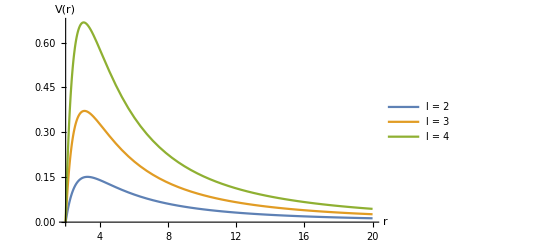

```mathematica
Plot[Evaluate@Table[Vtemp/.l->lval,{lval,{2,3,4}}],{r,2.001,20},PlotLegends->{"l = 2","l = 3","l = 4"},AxesLabel->{"r","V(r)"},PlotRange->All]
```